```mathematica
(*FD[m_,eta_]:=NIntegrate[x^m/(Exp[x-eta]+1),{x,0,Infinity}]*)
Clear[FD,etae]
```

```mathematica
F[m_,eta_]:=NIntegrate[x^m/(Exp[x-eta]+1),{x,0,Infinity}]
```

```mathematica
(* electron/positron pair annihilation to create neutrino/anti-neutrino pairs *)
```

```mathematica
sigma0=1.76*10^(-44)
sinsqTw=0.23
Cv=1/2+2*sinsqTw
Ca=1/2
C1C2e = (2/36)*((Cv-Ca)^2+(Cv+Ca)^2)
(* below factor of 4 is for fact that in Ruffert B10 has 4 species *)
C1C2other=(2/(9*4))*((Cv-Ca)^2+(Cv+Ca-2)^2)
Reenue2Reenux=(C1C2other)/(C1C2e)
```

1.76×10^-44

0.23

0.96

1/2

0.130178

0.0279556

0.214749

```mathematica
0.7/3.4
```

0.205882

```mathematica
0.7/3.64
```

0.192308

```mathematica
0.15/0.7
```

0.214286

```mathematica
T=T11*10^(11)
Eneg = 8*Pi/(h*c)^3*(kb*T)^4*FD[3,etae]
Epos = 8*Pi/(h*c)^3*(kb*T)^4*FD[3,-etae]
ETneg = 8*Pi/(h*c)^3*(kb*T)^5*FD[4,etae]
ETpos = 8*Pi/(h*c)^3*(kb*T)^5*FD[4,-etae]
ESneg = 8*Pi/(h*c)^3*(kb*T)^6*FD[5,etae]
ESpos = 8*Pi/(h*c)^3*(kb*T)^6*FD[5,-etae]

Reenue=C1C2e*sigma0*c/(me*c^2)^2*blockee*Eneg*Epos
Efactor=FullSimplify[(1/2)*(ETneg*Epos+Eneg*ETpos)/(Eneg*Epos)]
Qeenue =FullSimplify[ Reenue*Efactor]
Reenux=C1C2other*sigma0*c/(me*c^2)^2*blockeexx*Eneg*Epos
Qeenux =FullSimplify[ Reenux*Efactor]
```

100000000000 T11

1.16507×10^29 T11^4 FD[3,etae]

1.16507×10^29 T11^4 FD[3,-etae]

1.60857×10^24 T11^5 FD[4,etae]

1.60857×10^24 T11^5 FD[4,-etae]

2.22088×10^19 T11^6 FD[5,etae]

2.22088×10^19 T11^6 FD[5,-etae]

1.39096×10^36 blockee T11^8 FD[3,-etae] FD[3,etae]

(6.90329×10^-6 T11 FD[4,-etae])/FD[3,-etae]+(6.90329×10^-6 T11 FD[4,etae])/FD[3,etae]

blockee T11^9 (9.60222×10^30 FD[3,etae] FD[4,-etae]+9.60222×10^30 FD[3,-etae] FD[4,etae])

2.98708×10^35 blockeexx T11^8 FD[3,-etae] FD[3,etae]

blockeexx T11^9 (2.06207×10^30 FD[3,etae] FD[4,-etae]+2.06207×10^30 FD[3,-etae] FD[4,etae])

```mathematica
Clear[etae]
```

```mathematica
Reenue//.{etae->0}
```

NIntegrate::inumr: The integrand x^3/1 + ⅇ^etae + x has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand x^3/1 + ⅇ^-etae + x has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

4.49105×10^37 blockee T11^8

```mathematica
Reenux
```

2.98708×10^35 blockeexx T11^8 FD[3,-etae] FD[3,etae]

```mathematica
Reenue2Reenux
```

0.214749

```mathematica
.15/.7
```

0.214286

```mathematica
Efactor
```

(6.90329×10^-6 T11 FD[4,-etae])/FD[3,-etae]+(6.90329×10^-6 T11 FD[4,etae])/FD[3,etae]

```mathematica
Qnue=Qeenue//.{etae->0.0}//.{FD->F}
Qnux=Qeenux//.{etae->0.0}//.{FD->F}
(Qnue+Qnux*2)//.{blockee->1,blockeexx->1}
Qnux/Qnue
0.15/0.7
```

2.54595×10^33 blockee T11^9

5.46739×10^32 blockeexx T11^9

3.63942×10^33 T11^9

(0.214749 blockeexx)/blockee

0.214286

```mathematica
(* 3.64 agrees with corona paper *)
```

```mathematica
(* corona paper *)
```

```mathematica
1.39*10^(34)*(kb*T/(10*ergPmev))^9
```

3.64347×10^33 T11^9

```mathematica
(* BRT06 *)
```

```mathematica
Qeebt=9.7615*10^(24)*(kb*T/ergPmev)^9
```

2.55799×10^33 T11^9

```mathematica
Qmutaubt=4.1724*10^(24)*(kb*T/ergPmev)^9
each=Qmutaubt/2
```

1.09337×10^33 T11^9

5.46686×10^32 T11^9

```mathematica
Qeenux//.{etae->8.1513}//.{FD->F,T11->8.183*10^(-2)}
Reenux//.{etae->8.1513}//.{FD->F,T11->8.183*10^(-2)}
```

1.98478×10^22 blockeexx

2.99923×10^27 blockeexx

```mathematica
1.27332*10^(33) + 2*1.09378*10^(33)
```

3.46088×10^33

```mathematica
1.27332/3.4
```

0.374506

```mathematica
F[3,0.0]/F[2,0.0]
```

3.15137

```mathematica
(* PLASMON *)
```

```mathematica
gammap=gamma0*Sqrt[(1/3)*(Pi^2+3.0*etae^2)]
Clear[gammap]
sigma0=1.76*10^(-44)
sinsqTw=0.23
alpha=1.25
Cv=1/2+2*sinsqTw
Otherfactor=gamma^6*Exp[-gamma]*(1+gamma)*blocksq
alphastar=1/137.036
(* 2 below is because Ruffert B11 is for each anti/normal type *)
Rplasmonee = 2*Pi^3/(3*alphastar)*Cv^2*sigma0*c/(me*c^2)^2*(kb*T)^8/(h*c)^6*Otherfactor
Efactor = 0.5*kb*T*(2.0+gammap^2/(1+gammap))
Qplasmonee = Rplasmonee*Efactor
```

(gamma0 √(3. etae^2+π^2))/(√3)

1.76×10^-44

0.23

1.25

0.96

blocksq ⅇ^-gamma gamma^6 (1+gamma)

0.00729735

4.41606×10^37 blocksq ⅇ^-gamma gamma^6 (1+gamma) T11^8

6.90329×10^-6 (2.+gammap^2/(1+gammap)) T11

3.04853×10^32 blocksq ⅇ^-gamma gamma^6 (1+gamma) (2.+gammap^2/(1+gammap)) T11^9

```mathematica
Cv
```

0.96

```mathematica
0.5+2*0.23
```

0.96

```mathematica
Rplasmonee2Rplasmonxx=(2*(Cv-1)^2)/(2*4*Cv^2/4)
```

0.00173611

```mathematica
1/(Rplasmonee2Rplasmonxx)
```

576.

```mathematica
163*3
```

489

```mathematica
(* free neutron or proton rates *)
```

```mathematica
sigma0=1.76*10^(-44)
alpha=1.25
sinsqTw=0.23
Csn=(1+5*alpha^2)/24
Cv=1/2+2*sinsqTw
Csp=(4*(Cv-1)^2+5*alpha^2)/24
T=T11*10^(11)
rhob=rho10*10^(10)
sigmasn=Csn*sigma0*(kb*T/(me*c^2))^2*Esqnu
sigmasp=Csp*sigma0*(kb*T/(me*c^2))^2*Esqnu
nb=rhob/mb
Yn=(1-Ye)
Yp=Ye
Ynn=Yn/factor1
Ypp=Yp/factor2
nn=nb*Ynn
np=nb*Ypp
Ksn=sigmasn*nn
Ksp=sigmasp*np
```

1.76×10^-44

1.25

0.23

0.367188

0.96

0.325788

100000000000 T11

10000000000 rho10

(6.4625×10^-23 Esqnu kb^2 T11^2)/(c^4 me^2)

(5.73386×10^-23 Esqnu kb^2 T11^2)/(c^4 me^2)

(10000000000 rho10)/mb

1-Ye

Ye

(1-Ye)/factor1

Ye/factor2

(10000000000 rho10 (1-Ye))/(factor1 mb)

(10000000000 rho10 Ye)/(factor2 mb)

(6.4625×10^-13 Esqnu kb^2 rho10 T11^2 (1-Ye))/(c^4 factor1 mb me^2)

(5.73386×10^-13 Esqnu kb^2 rho10 T11^2 Ye)/(c^4 factor2 mb me^2)

```mathematica
sigmasb
```

0.000056712

```mathematica
sigmasb*10^5
```

5.6712

```mathematica
(* photons *)
Kes = 0.4*Ye *rhob
Kff=0.645*10^(23)*(Ye^2*1*Z)*rhob^2*T^(-3.5)
Kbf=4.34*10^(25)*Xnuc*(1.0)*rhob^2*T^(-3.5)
```

4.×10^9 rho10 Ye

(20396.7 rho10^2 Ye^2 Z)/T11^3.5

(1.37243×10^7 rho10^2 Xnuc)/T11^3.5

```mathematica
ne=Ye*nb
mA =A*mb
ni=rhoA10*10^(10)/mA
Lambdaff = 1.42*10^(-27)*Z^2*ne*ni*T^(1/2)
```

5.97452×10^33 rho10 Ye

1.67377×10^-24 A

(5.97452×10^33 rhoA10)/A

(1.60286×10^46 rho10 rhoA10 √T11 Ye Z^2)/A

```mathematica
Knnu=(1+3*alpha^2)/4*sigma0*etanp*(kb*T/(me*c^2))^2*FD[4+j,etanue]/FD[2+j,etanue]*blocknnu
```

(7.11725×10^-42 blocknnu etanp T11^2 FD[4+j,etanue])/FD[2+j,etanue]

```mathematica
Knnu//.{etanp->nn}
```

(4.25221×10^-8 blocknnu rho10 T11^2 (1-Ye) FD[4+j,etanue])/(factor1 FD[2+j,etanue])

```mathematica
(* Burrows & Thompson 2002, equation 103 and 104 for pair annihilation *)
Qe=9.7615
Qx=1/2*4.1724
Qx/Qe
0.15/0.7
```

9.7615

2.0862

0.213717

0.214286

```mathematica
ffactor=(FD[4,etae]*FD[3,-etae]+FD[4,-etae]*FD[3,etae])/(2*FD[4,0]*FD[3,0])
Qe=9.7615*10^(24)*(kb*T/ergPmev)^9*ffactor
Qx=0.5*4.1724*10^(24)*(kb*T/ergPmev)^9*ffactor
```

(FD[3,etae] FD[4,-etae]+FD[3,-etae] FD[4,etae])/(2 FD[3,0] FD[4,0])

(1.27934×10^33 T11^9 (FD[3,etae] FD[4,-etae]+FD[3,-etae] FD[4,etae]))/(FD[3,0] FD[4,0])

(2.73418×10^32 T11^9 (FD[3,etae] FD[4,-etae]+FD[3,-etae] FD[4,etae]))/(FD[3,0] FD[4,0])

```mathematica
Qe//.{FD->F,etae->0}
Qx//.{FD->F,etae->0}
```

2.55869×10^33 T11^9

5.46836×10^32 T11^9

```mathematica
56*3.89025*10^(-8)
```

2.17854×10^-6

```mathematica
661+276
```

937

```mathematica
3.89*10^(-8)*56
```

2.1784×10^-6

```mathematica
N[2*Sqrt[3],25]
```

3.464101615137754587054893

```mathematica
N[1/Sqrt[3],25]
```

0.5773502691896257645091488

```mathematica
2^(31)
```

2147483648

```mathematica
solgf=Solve[sigma0==Gf^2*(me*c^2)^2/(Pi*(hbar*c)^4),Gf]
mygf=solgf[[2,1,2]]
sinsqtw=1/4
De=1+4*sinsqtw+8*sinsqtw^2
Dx=1-4*sinsqtw+8*sinsqtw^2
Qee=mygf^2/(9*Pi)*De*em*ep*(wm+wp)
Qxx=mygf^2/(9*Pi)*Dx*em*ep*(wm+wp)
```

{{Gf→-(hbar^2 √π √sigma0)/me},{Gf→(hbar^2 √π √sigma0)/me}}

(hbar^2 √π √sigma0)/me

1/4

5/2

1/2

(5 em ep hbar^4 sigma0 (wm+wp))/(18 me^2)

(em ep hbar^4 sigma0 (wm+wp))/(18 me^2)

```mathematica
(* BRT06 *)
```

```mathematica
rho14=rho/10^(14)
rho=rho13*10^(13)
rho13=rho10*10^(10)/10^(13)
Qnb=1.04*10^(30)*0.5*(Xn*rho14)^2*(kb*T/ergPmev)^5.5
Qnb*3
```

rho13/10

10000000000000 rho13

rho10/1000

7.25387×10^26 rho10^2 T11^5.5 Xn^2

2.17616×10^27 rho10^2 T11^5.5 Xn^2

```mathematica
h=hbar*(2*Pi)
arad=8*Pi^5*kb^4/(15*c^3*h^3)
prad=arad*T^4/3
gam=4/3
urad=prad/(gam-1)
srad=(urad+prad)/(kb*T)
```

2 hbar π

(kb^4 π^2)/(15 c^3 hbar^3)

(kb^4 π^2 T^4)/(45 c^3 hbar^3)

4/3

(kb^4 π^2 T^4)/(15 c^3 hbar^3)

(4 kb^3 π^2 T^3)/(45 c^3 hbar^3)

```mathematica
prad
```

(kb^4 π^2 T^4)/(45 c^3 hbar^3)

```mathematica
Solve[srad==x
```

```mathematica
T=T11*10^(11)
arad*T^4
```

100000000000 T11

7.56591×10^29 T11^4

```mathematica
(* modified URCA from Shapiro Book eq 15.5.22 *)
```

```mathematica
rhonuc=2.8*10^(14)
rho=rho10*10^(10)
T9=T/10^9
T=T11*10^(11)
Q=1.2*10^(20)*(rho/rhonuc)^(2/3)*T9^8*(1+F)
```

2.8×10^14

10000000000 rho10

100 T11

100000000000 T11

1.3014×10^33 (1+F) rho10^(2/3) T11^8

```mathematica
corr=(5.3*10^(39))/(8.5*10^(38))
```

6.23529

```mathematica
Q*corr
```

8.11458×10^33 (1+F) rho10^(2/3) T11^8

```mathematica
(mb-mn)*c^2/ergPmev
```

-0.646668

1/(1+ⅇ^(-A+x))

-2 PolyLog[3,-ⅇ^A]

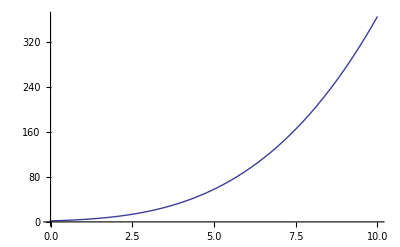

```mathematica
f=1/(1+Exp[x-A])
g=Integrate[f*x^2,{x,0,Infinity}]
Plot[g,{A,0,10}]
```

```mathematica
60*60
```

3600

```mathematica
x=2*2.54
```

5.08

```mathematica
(x-3.5)/2/2.54
(x-4.5)/2/2.54
```

0.311024

0.114173

```mathematica
5/16.
```

0.3125

```mathematica
2.0/16.0
```

0.125

```mathematica
GF=2.302*10^(-22)/(ergPmev)^3
```

```mathematica
(* BRT06 *)
GF=1.436*10^(-49)
sigma0=4*GF^2*(me*c^2)^2/(Pi*(hbar*c)^4)
```

0.0000559724

1.436×10^-49

1.76153×10^-44

1.76153×10^-44

```mathematica
GF=2.302*10^(-22)
GF^2/Pi
K1=GF^2*c^3/(2*Pi^3*c^2*hbar^3)
taun=885.7
(1.636*(me*c^2)^5*taun)^(-1.0)
```

2.302×10^-22

1.68679×10^-44

2.18435×10^46

885.7

1.8762×10^27

```mathematica
GF=1.1664*10^(-11)
GF^2
```

1.1664×10^-11

1.36049×10^-22

```mathematica
(* E=hbar*nu=hbar c/lambda , hbar*c=E*lambda *)
```

```mathematica
mevtosec=1.519*10^(21)
mevtosec=ergPmev/((hbar*c)/c)
GF=1.1664*10^(-11)
mev2k=1.16041*10^(10)
mev2k=ergPmev/kb
tmev=T11*10^(11)/mev2k
T11=T/10^(11)
(* 1/s *)
gamma=GF^2/(2*Pi^3)*tmev^5*mevtosec
gamma/(kb*T)^5*(hbar*c)^5/c
mev4toecc=2.085*10^(26)
mev4toecc=ergPmev^4/(hbar*c)^3
L=(hbar*c)/(me*c^2)
gamma=GF^2/(2*Pi^3)/mev4toecc*(hbar*c)/L
```

1.519×10^21

1.51927×10^21

1.1664×10^-11

1.16041×10^10

1.16044×10^10

8.61739×10^-11 T

T/100000000000

1.5839×10^-53 T^5

3.32631×10^-67

2.085×10^26

2.08521×10^26

3.8616×10^-11

8.61382×10^-57

```mathematica
L=(hbar*c)/(me*c^2)
GF=1.16637*10^(-11) (* 1/MeV^2 *)
GF/ergPmev^2*(hbar*c)^2*L/(4*Pi)
GF*1000^2 (* 1/GeV^2 *)
GFcgs=(GF/ergPmev^2)*(hbar*c)^3
```

3.8616×10^-11

1.16637×10^-11

1.39562×10^-44

0.0000116637

1.43584×10^-49

```mathematica
GF=1.16637*10^(-11) (* 1/MeV^2 *)
GFcgs=(GF/ergPmev^2)*(hbar*c)^3
ga=-1.18
f=GFcgs^2*(1+3ga^2)/(2*Pi^3*c^2*hbar^3)*c^5
taun=885.7
(1.636*taun)^(-1)
```

1.16637×10^-11

1.43584×10^-49

-1.18

3.95424×10^13

885.7

0.000690129

```mathematica
costhetac
```

0.974213

1.43584×10^-49

1.67149×10^-44

```mathematica
(* my version *)
GF=1.16637*10^(-11) (* 1/MeV^2 *)
GFcgs=(GF/ergPmev^2)*(hbar*c)^3
sigma0=4*GFcgs^2*costhetac^2*(me*c^2)^2/(Pi*(hbar*c)^4)
myK1=sigma0*c/(2*Pi^2*(hbar*c)^3*(me*c^2)^2)
myK1withtemp=myK1*(kb*T)^5
```

1.16637×10^-11

1.43584×10^-49

1.67149×10^-44

1.19851×10^27

6.01275×10^-53 T^5

```mathematica
ga=-1.23
myK1*(1+3*ga^4)/4
```

-1.23

2.35706×10^27

```mathematica
1/alpha
```

137.053

```mathematica
(* kaz version *)
GF=1.16637*10^(-11) (* 1/MeV^2 *)
tmev=kb*T/ergPmev
mevtosec=1.519*10^(21)
mevtosec=ergPmev/((hbar*c)/c)
K1withtemp=4*(GF^2)/(2*Pi^3)*tmev^5*mevtosec
(* doesn't include (1+3ga^2)/4 term for np procs *)
```

1.16637×10^-11

8.61739×10^-11 T

1.519×10^21

1.51927×10^21

6.33528×10^-53 T^5

```mathematica
(* agreement! *)
```

```mathematica
GF=1.16637*10^(-11) (* 1/MeV^2 *)
tmev=kb*T/ergPmev
mevtosec=1.519*10^(21)
mevtosec=ergPmev/((hbar*c)/c)
fakerate=4*GF^2/(2*Pi^3)*tmev^5*mevtosec
fakesigma0=fakerate/c*(hbar*c)^3/(me*c^2)^3/(kb*T)^5*(me*c^2)^5*(2*Pi^3)/Pi
```

1.16637×10^-11

8.61739×10^-11 T

1.519×10^21

1.51927×10^21

6.33528×10^-53 T^5

1.76115×10^-44

```mathematica
myK1=sigma0
```

1.43584×10^-49

0.227591

0.949091

1.67149×10^-44

```mathematica
me
mealso
```

9.10938×10^-28

9.10938×10^-28

```mathematica
SinTWsq=0.228
mw=37.3/Sqrt[SinTWsq] (* GeV *)
GF=alpha/(4*Sqrt[2]*mw^2*SinTWsq)*(Pi*4)
```

0.228

78.1163

0.00001165

```mathematica
1/alpha
```

137.053

```mathematica
alpha
```

0.00729642

```mathematica
mev4toecc=2.085*10^(26)
mev4toecc=ergPmev^4/(hbar*c)^3
GF=1.1664*10^(-11) (* 1/MeV^2 *)
GF/ergPmev^2
```

2.085×10^26

2.08521×10^26

1.1664×10^-11

4.54388

```mathematica
hbar*c^2
```

9.47803×10^-7

2.085×10^26

2.08521×10^26

```mathematica
GF=1.1664*10^(-11) (* in MeV^{-2} *)
(GF/ergPmev^2)*(hbar*c)^2*(me*c^2)
GF
```

1.1664×10^-11

3.71836×10^-39

1.1664×10^-11

```mathematica
me*c^2
```

8.1871×10^-7

```mathematica
L=(hbar*c)/(me*c^2)
GF=1.436*10^(-49)/ergPmev*
```

3.8616×10^-11

5.16113×10^-75

0.00048029